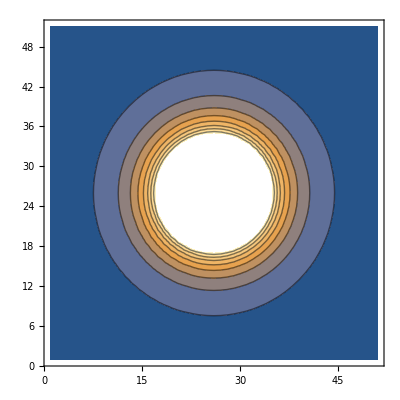

```mathematica
{mx,my,mz} = Normalize[{0,0,5}];
{cx,cy,cz} ={0,0,0.1};
z= 0;
ListContourPlot[Table[Norm[1/EuclideanDistance[{x,y,z},{cx,cy,cz}]^3(3*-)*{mx,my,mz}],{x,-5,5,.2},{y,-5,5,.2}]]
```